## Study of the deformed potential with quadrupole character of a single-particle j moving in a field generated by the triaxial rotor R

```mathematica
ClearAll["Global`*"]
```

### Declare the color function which will be used for DensityPlot

```mathematica
CoolColor[ z_ ] :=RGBColor[z,1-z,1];
```

### Constants

```mathematica
A=163;
β=0.38;
j=13/2;
γ=20;
```

```mathematica
rad[degs_]:=degs*π/180;
```

The Spherical Harmonics Y_lm(θ,φ)

```mathematica
YLM[l_,m_]:=SphericalHarmonicY[l,m,θ,φ];
```

The coupling constant C=195/(j(j+1))A^(-1/3)β_2 and the coupling factor from the potential V(β_2,γ)

```mathematica
Cpl[A_,β_,j_]:=195/(j(j+1))A^(-1/3)*β;
CplV[A_,β_]:=206/A^(1/3)*β;
c=CplV[A,β];
```

The single-particle potential can be expressed by using the expression for the γ-deformed Nillson potential

-Graphics-

```mathematica
Vsp[A_,β_,γ_]:=CplV[A,β]*(Cos[γ]*YLM[2,0]+Sin[γ]/Sqrt[2](YLM[2,2]+YLM[2,-2]));
```

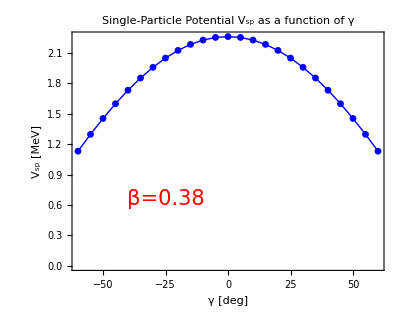

```mathematica
listPotential[β_]:=ListPlot[Table[{x,Vsp[A,β,rad[x]]/.{θ->π/4,φ->π/4}},{x,-60,60,5}],Frame->True,Axes->False,AspectRatio->0.8,Joined->True,FrameLabel->{"γ [deg]","V_sp [MeV]"},PlotLabel->Style["Single-Particle Potential V_sp\nas a function of γ",15,Italic],PlotMarkers->{Automatic, Small},PlotStyle->{Blue,Thick},FrameStyle->Directive[Black,Thick],LabelStyle->{19,Bold,Black,FontFamily->"Times"},Epilog->Inset[Style[StringTemplate["β=``"][β],Red,21,FontFamily->"Times"],Scaled[{0.3,0.3}]]];
listPotential[β]
```

### Function for making a grid of plots

```mathematica
makeGrid[plotList_]:=Grid[{Table[Show[plotList[[i]]],{i,1,Length[plotList]/2}],Table[Show[plotList[[i]]],{i,Length[plotList]/2+1,Length[plotList]}]},Frame->All];
```

### Function for exporting a graphics object into a custom location

```mathematica
save[file_,object_]:=Export[StringTemplate["/Users/robertpoenaru/Library/Mobile Documents/com~apple~CloudDocs/Work/Pipeline/DevWorkspace/Github/physics-code-collection/Code-Collection/Quadrupole-Deformed-MeanField/``.pdf"][file],object,ImageResolution->1200];
```

### Function for generating a single contour plot with the single-particle deformed potential

Parameters for the contour and density plots of the single-particle deformed potential V are β,γ

```mathematica
makeContour[β_,γ_]:=ContourPlot[Vsp[A,β,rad[γ]],{θ,0,π},{φ,0,2π},FrameStyle->Directive[Black,Thick],AspectRatio->1,ColorFunction->"BlueGreenYellow",Frame->True,FrameLabel->{"θ [rad]","φ [rad]"},LabelStyle->{18,FontFamily->"Times",Bold,Black},Contours->Automatic,ContourStyle->{Black,Opacity[1]},(*ContourLabels->(Style[Text[#3,{#1,#2}],Red,Bold,17,FontFamily->"Times"]&),*)PlotLegends->Automatic,ImageSize->Medium,PlotRange->Full,PlotLabel->Style[StringTemplate["Single-particle potential V_sp\nj=π(i_(13/2))  β=``  γ=(``)^0"][β,γ],15,Black,Italic,Plain]];
makeDense[β_,γ_]:=DensityPlot[Vsp[A,β,rad[γ]],{θ,0,π},{φ,0,2π},ColorFunction->"DeepSeaColors",FrameStyle->Directive[Black,Thick],AspectRatio->1,ColorFunction->"BlueGreenYellow",Frame->True,FrameLabel->{"θ [rad]","φ [rad]"},LabelStyle->{18,FontFamily->"Times",Bold,Black},PlotLegends->Automatic,ImageSize->Medium,PlotRange->Full,PlotLabel->Style[StringTemplate["Single-particle potential V_sp\nj=π(i_(13/2))  β=``  γ=(``)^0"][β,γ],15,Black,Italic,Plain]];
```

## Study the β-variation of the single-particle potential

### Contour-Plot

```mathematica
cpbeta1=makeContour[0.1,20];
cpbeta2=makeContour[0.15,20];
cpbeta3=makeContour[0.25,20];
cpbeta4=makeContour[0.38,20];
contoursbeta={cpbeta1,cpbeta2,cpbeta3,cpbeta4};
contourbeta=makeGrid[contoursbeta];
save["cp-Vsp-betaDependece",contourbeta];
```

### Density-Plot

```mathematica
dpbeta1=makeDense[0.1,20];
dpbeta2=makeDense[0.15,20];
dpbeta3=makeDense[0.25,20];
dpbeta4=makeDense[0.38,20];
denseplotsbeta={dpbeta1,dpbeta2,dpbeta3,dpbeta4};
densebeta=makeGrid[denseplotsbeta];
save["dp-Vsp-betaDependece",densebeta];
```

## Study the γ-variation of the single-particle potential

### Contour-Plot

```mathematica
cpgamma1=makeContour[0.30,-30];
cpgamma2=makeContour[0.30,10];
cpgamma3=makeContour[0.30,45];
cpgamma4=makeContour[0.30,60];
contoursgamma={cpgamma1,cpgamma2,cpgamma3,cpgamma4};
contourgamma=makeGrid[contoursgamma];
save["cp-Vsp-gammaDependece",contourgamma];
```

### Density-Plot

```mathematica
dpgamma1=makeDense[0.30,-30];
dpgamma2=makeDense[0.30,10];
dpgamma3=makeDense[0.30,45];
dpgamma4=makeDense[0.30,60];
denseplotsgamma={dpgamma1,dpgamma2,dpgamma3,dpgamma4};
densegamma=makeGrid[denseplotsgamma];
save["dp-Vsp-gammaDependece",densegamma];
```

## Graphical representation of the spherical harmonics for the triaxial potential -Graphics-

```mathematica
SphericalPlot3D[Re[SphericalHarmonicY[2,-2,θ,φ]]+Re[SphericalHarmonicY[2,2,θ,φ]]+SphericalHarmonicY[2,0,θ,φ],{θ,0,π},{φ,0,2π}]
```

-Graphics3D-